1. Renormalization Group Recursive Equations Setup

```mathematica
dim=8;
Clear[μ,η];
A[6]=B[6]=μ;
A[7]=B[7]=η;
Z0[x0_,x1_,x2_,x3_,x4_]:=μ^(-(x0*x3+x1*x4)/2)*η^(-(x1+x3)/2)*Exp[-2*A[0]]*A[1]^(-((x0+x1)+(x1+x2)+(x2+x3)+(x3+x4))/2)*A[2]^(-((x0+x2)+(x2+x4))/2)*A[3]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/2)*A[4]^(-(x0*x2+x2*x4)/2)*A[5]^(-(x0*x1*x2+x2*x3*x4)/2)
Z1[x0_,x2_,x4_]:=Exp[-B[0]]*B[1]^(-((x0+x2)+(x2+x4))/2)*B[2]^(-(x0+x4)/2)*B[3]^(-(x0*x2+x2*x4)/2)*B[4]^(-(x0*x4)/2)*B[5]^(-x0*x2*x4/2)
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
i=0;
For[x0=-1,x0<=1,x0+=2,
For[x2=-1,x2<=1,x2+=2,
For[x4=-1,x4<=1,x4+=2,
leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];
]
]
]
(*Equates the unrenormalized with the renormalized variables*)
req[0]==leq[0];
req[1]==leq[1];
req[2]==leq[2];
req[3]==leq[3];
req[4] == leq[4];
req[5] ==leq[5] ;
req[6] ==leq[6] ;
req[7] ==leq[7] ;
SB[0]=Simplify[Solve[Simplify[(Factor[leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7]])^(-1/8),Assumptions->B[0]>0]==Simplify[(Factor[req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7]])^(-1/8),Assumptions->η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0],B[0]],Assumptions->C[1]==0&&η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0][[1]];
SB[0]={B[0]-> 2*A[0]+(B[0]/.SB[0]/.A[0]->0)};
SB[1]=Simplify[Part[Solve[Simplify[((leq[0]*leq[1]*leq[1]*leq[5])^(1/4)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0)]==Simplify[((req[0]*req[1]*req[1]*req[5])^(1/4)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[1]],1]];
SB[2]=Simplify[Part[Solve[Simplify[((leq[2]/leq[5]/leq[1])^(1/4)*(leq[0]/leq[1]*leq[2]*leq[3]*leq[4]/leq[5]*leq[6]/leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0&& B[2]>0&& B[4]>0&& B[5]>0)]==Simplify[((req[2]/req[5]/req[1])^(1/4)*(req[0]/req[1]*req[2]*req[3]*req[4]/req[5]*req[6]/req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[2]],1]];
SB[3]=Simplify[Part[Solve[Simplify[(leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->(B[0]>0 && B[3]>0)]==Simplify[(req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[3]],1]];
SB[4]=Simplify[Part[Solve[Simplify[(leq[1]*leq[3])/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->B[0]>0]==Simplify[(req[1]*req[3])/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[4]],1]];
SB[5]=Simplify[Part[Solve[Simplify[(leq[0]/leq[1]/leq[2]*leq[3])^(1/2)*((leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4)),Assumptions->(B[3]>0 && B[5]>0 && B[0]>0)]==Simplify[(req[0]/req[1]/req[2]*req[3])^(1/2)*((req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[5]],1]];
SBT=Table[Part[Factor[SB[n]],1],{n,0,5}];
```

```mathematica
SBT
```

{B[0]→2 A[0]+Log[(η μ A[1]^2 A[3] A[5])/(√((η μ A[1]^2+A[5]) (η A[1]^2+μ A[5])) ((μ A[3]^2+η A[1]^2 A[5]) (A[3]^2+η μ A[1]^2 A[5]) (μ+η A[1]^2 A[3]^2 A[5]) (1+η μ A[1]^2 A[3]^2 A[5]))^(1/4))],B[1]→(A[1] A[2] √(μ A[3]^4+η A[1]^2 A[3]^2 A[5]+η μ^2 A[1]^2 A[3]^2 A[5]+η^2 μ A[1]^4 A[5]^2))/(η^2 A[1]^4 A[3]^4 A[5]^2+η^2 μ^4 A[1]^4 A[3]^4 A[5]^2+η μ A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+η μ^3 A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+μ^2 (η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+A[3]^4 (1+η^2 A[1]^4 A[5]^2)^2))^(1/4),B[2]→1/(√((η μ A[1]^2+A[5])/(η A[1]^2+μ A[5])) (((A[3]^2+η μ A[1]^2 A[5]) (1+η μ A[1]^2 A[3]^2 A[5]))/(μ^2 A[3]^2+η μ A[1]^2 (1+A[3]^4) A[5]+η^2 A[1]^4 A[3]^2 A[5]^2))^(1/4)),B[3]→A[3] A[4] √((η^2 μ A[1]^4+η A[1]^2 A[5]+η μ^2 A[1]^2 A[5]+μ A[5]^2)/(μ A[3]^2+η A[1]^2 A[5]+η μ^2 A[1]^2 A[3]^4 A[5]+η^2 μ A[1]^4 A[3]^2 A[5]^2)),B[4]→((A[3]^2+η μ A[1]^2 A[5]) (μ+η A[1]^2 A[3]^2 A[5]))/(√(η^2 A[1]^4 A[3]^4 A[5]^2+η^2 μ^4 A[1]^4 A[3]^4 A[5]^2+η μ A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+η μ^3 A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+μ^2 (η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+A[3]^4 (1+η^2 A[1]^4 A[5]^2)^2))),B[5]→((η μ A[1]^2+A[5]) (μ A[3]^2+η A[1]^2 A[5]) (μ+η A[1]^2 A[3]^2 A[5]))/((η A[1]^2+μ A[5]) √(η^2 A[1]^4 A[3]^4 A[5]^2+η^2 μ^4 A[1]^4 A[3]^4 A[5]^2+η μ A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+η μ^3 A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+μ^2 (η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+A[3]^4 (1+η^2 A[1]^4 A[5]^2)^2)))}

2. Recursive Equation Setup

```mathematica
Clear[μ,η]
SIC={B[0]->0,B[1]->η,B[2]->η,B[3]->μ,B[4]->1,B[5]->1};
Sκλ={A[0]->lnC,A[1]->1,A[2]->1,A[3]->κ,A[4]->λ,A[5]->1}
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,dim-1}];
RG:=SAT=Table[A[n]->B[n]/.Simplify[SBT/.SAT],{n,0,dim-1}];
```

{A[0]→lnC,A[1]→1,A[2]→1,A[3]→κ,A[4]→λ,A[5]→1}

```mathematica
k[μ_]:=A[3] A[4] √((η^2 μ A[1]^4+η A[1]^2 A[5]+η μ^2 A[1]^2 A[5]+μ A[5]^2)/(μ A[3]^2+η A[1]^2 A[5]+η μ^2 A[1]^2 A[3]^4 A[5]+η^2 μ A[1]^4 A[3]^2 A[5]^2));
l[μ_]:=((A[3]^2+η μ A[1]^2 A[5]) (μ+η A[1]^2 A[3]^2 A[5]))/(√(η^2 A[1]^4 A[3]^4 A[5]^2+η^2 μ^4 A[1]^4 A[3]^4 A[5]^2+η μ A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+η μ^3 A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+μ^2 (η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+A[3]^4 (1+η^2 A[1]^4 A[5]^2)^2)))
```

```mathematica
Clear[μ,,η,κ,λ]
,η=1
A[3] A[4] √((η^2 μ A[1]^4+η A[1]^2 A[5]+η μ^2 A[1]^2 A[5]+μ A[5]^2)/(μ A[3]^2+η A[1]^2 A[5]+η μ^2 A[1]^2 A[3]^4 A[5]+η^2 μ A[1]^4 A[3]^2 A[5]^2))/.Sκλ
```

```mathematica
Clear[μ,η];
InitRG;
η=1;
μ=0.1;
RG;
SAT
RG;
SAT
κ=A[3]/.SAT
```

{A[0]→-3.59734,A[1]→1.,A[2]→1.,A[3]→0.0010989,A[4]→0.10989,A[5]→1.,0.1→0.1,1→1}

{A[0]→-15.2547,A[1]→1.,A[2]→1.,A[3]→0.000132834,A[4]→0.100001,A[5]→1.,0.1→0.1,1→1}

0.000132834

0.000132834

{{3.85714,0.428571},{0.144902,0.391771},{0.213617,2.84198},{2.13598,2.6789},{1.55838,0.514897},{0.387371,0.655174},{0.700044,2.1722},{2.46238,1.41287},{0.725178,0.472295},{0.531489,1.36787},{1.57408,1.77677},{1.32656,0.649543},{0.54889,0.758011},{0.874159,1.73401},{1.84154,1.14326},{0.753679,0.571986},{0.63769,1.31949},{1.51612,1.53456},{1.17863,0.671063},{0.612236,0.849376},{0.97909,1.58853},{1.60513,1.02135},{0.751216,0.638816},{0.7128,1.32356},{1.49499,1.38975},{1.07861,0.679428},{0.652834,0.927223},{1.06263,1.50365},{1.45669,0.941111},{0.744468,0.695365},{0.777673,1.33482},{1.47539,1.28087},{1.00382,0.687457},{0.686143,0.996192},{1.13337,1.43874},{1.34385,0.882754},{0.739373,0.748842},{0.838894,1.34343},{1.44894,1.19044},{0.945364,0.698717},{0.717758,1.05775},{1.193,1.38092},{1.25049,0.839365},{0.737717,0.801897},{0.898816,1.34624},{1.41374,1.11224},{0.899039,0.714504},{0.75025,1.11196},{1.24116,1.32517},{1.17034,0.80771},{0.74009,0.85528},{0.957906,1.34221},{1.37042,1.04392},{0.862574,0.735293},{0.784932,1.15839},{1.27689,1.26955},{1.10065,0.785976},{0.746682,0.908756},{1.01557,1.33111},{1.32075,0.984672},{0.834574,0.761152},{0.822437,1.19646},{1.29937,1.21365},{1.04004,0.773009},{0.757551,0.961515},{1.07052,1.31313},{1.26698,0.934197},{0.814075,0.791859},{0.862917,1.22575},{1.3083,1.15794},{0.987739,0.768004},{0.772711,1.01241},{1.12108,1.2887},{1.2114,0.89233},{0.80035,0.826933},{0.906103,1.24605},{1.3041,1.10336},{0.943223,0.770345},{0.792156,1.06014},{1.16536,1.25845},{1.15608,0.858868},{0.79282,0.865649},{0.95132,1.25743},{1.28798,1.05114},{0.906085,0.779512},{0.815836,1.10339},{1.20154,1.22318},{1.10274,0.833545},{0.791018,0.907043},{0.997505,1.26018},{1.26176,1.0025},{0.875965,0.795007},{0.843622,1.14094},{1.22806,1.18392},{1.05273,0.816041},{0.794568,0.949944},{1.04325,1.25478},{1.22768,0.958561},{0.852514,0.816288},{0.875248,1.17182}}

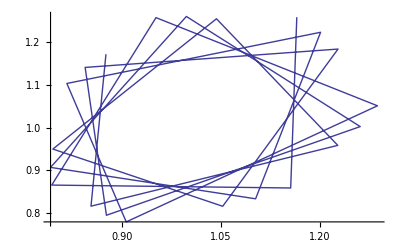

```mathematica
Clear[μ,η]
kmax=100;
InitRG;
η=N[1.0,100];
μ=N[3.0,100];
λκ=ConstantArray[0,{kmax,2}];
For[i=1,i<=kmax,i+=1,
RG;
Part[λκ,i][[1]]=A[3]/.SAT;
Part[λκ,i][[2]]=A[4]/.SAT;
]
λκ
ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-20,kmax}],Joined->True]
```

2.1 Recursive Equation Check

3. One Point Functions: IE and Mag

3.0 Ground State

3.1 Internal Energy

3.2 Magnetization vs H (big)

3.3 Magnetization vs H (small)

4. Two Point Functions : Cv and χ

4.1 Specific Heat Cv

4.2 Susceptibility χ